## The nuclear Coulomb potential

### The protons interact via the Coulomb force. The Coulomb potential inside and outside a homogeneous charge of radius R=r_0 A^(1/3) is as follows:

```mathematica
Subscript[ϵ, 0]=8.854*10^-12;
e=1;
```

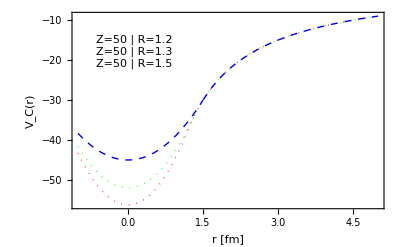

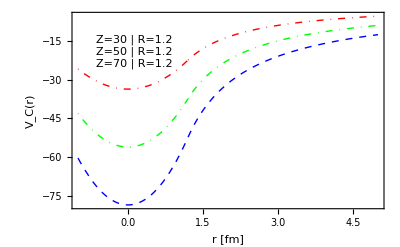

```mathematica
VC[r_,Z_,R_]:=Piecewise[{{Z*e^2/(4π*Subscript[ϵ, 0]*R)(1/2 r^2/R^2-3/2), r<R}, {-Z e^2/(4π*Subscript[ϵ, 0]*r), r>R}}];
plotC[Z_,R_,xcol_]:=Plot[VC[x,Z,R]/10^10,{x,-1,5},PlotStyle->{Thick,xcol,RandomChoice[{Dashed,Dotted,DotDashed}]},Frame->True,Axes->False,FrameLabel->{"r [fm]","V_C(r)"},LabelStyle->{FontFamily->"Times",18,Black,Bold},PlotLegends->Placed[Style[StringTemplate["Z=`` | R=``"][Z,R],Bold,xcol,Italic],{0.2,0.8}],PlotRange->All];
Show[plotC[50,1.2,Red],plotC[50,1.3,Green],plotC[50,1.5,Blue]]
Show[plotC[30,1.2,Red],plotC[50,1.2,Green],plotC[70,1.2,Blue]]
```